# Orbigraphs: Defining a Graph-Theoretic Analog to Riemannian Orbifolds

## Sam Stewart and Colin Gavin Lewis & Clark College - Portland, OR | -Graphics-

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<"Orbigraphs.m"

degenerateKStarEdges[adj_]:=degenerateKStarEdgesInner[adj,#1,#2]&
degenerateKStarEdgesInner[adj_,pts_List,e_]:=Module[{bumps,es,normal},
es=adj⟦e⟦1⟧,e⟦2⟧⟧;
If[es<2,Return[{Arrowheads[0.08],Arrow[pts]}]];
normal=Cross[pts⟦2⟧-pts⟦1⟧];
bumps=Table[normal*(n 0.4/(es-1)-0.2),{n,0,es-1}];
{Arrowheads[0.08]}~Join~(Arrow[BezierCurve[{pts⟦1⟧,Mean@pts+#,pts⟦2⟧}]]&/@bumps)
];
```

## Manifolds and Orbifolds

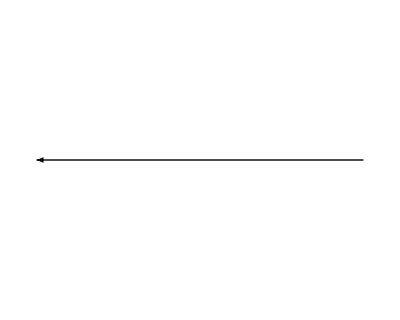
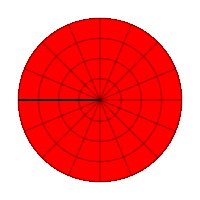
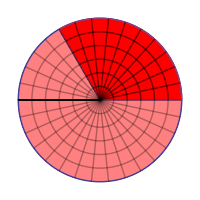
Manifold | -Graphics3D- | -Graphics- | -Graphics-
D^2
Orbifold | -Graphics3D- | -Graphics- | -Graphics-
ℤ_3 ⟳ D^2

```mathematica
s=RevolutionPlot3D[{Sqrt[1-t^2],t},{t,-1,0.5},{θ,0,2π},PlotStyle->Blue,PlotRange->{{-1,1},{-1,1},{-1,1}},Mesh->{9,15}];
c=RevolutionPlot3D[{Sqrt[1-t^2],t},{t,0.5,1},{θ,0,2π},PlotStyle->Red,Mesh->{3,15}];
sphere=Show[s,c,ImageSize->{200,200},Axes->False,Boxed->False,ViewVector->{0,4,2}];
maniChart=Column[{RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1},PlotStyle->Red,Mesh->{3,15},Frame->False,Axes->False,MeshFunctions->{Norm[{#1,#2}]&,ArcTan[#1,#2]&},PlotPoints->100,ImageSize->{200,200}],
Text[Style["D^2",Medium]]},Center];

teardrop=Piecewise[{{1/Sqrt[3]*x,x≤Sqrt[3]},{Sqrt[4/3-(x-4/Sqrt[3])^2],Sqrt[3]<x≤2*Sqrt[3]}}];
cone=RevolutionPlot3D[{teardrop,-x},{x,0,1},{θ,0,2π},Mesh->{5,10},PlotRange->{{-2,2},{-2,2},{-4,0}},PlotStyle->Red];
bulb=RevolutionPlot3D[{teardrop,-x},{x,1,2Sqrt[3]},{θ,0,2π},Mesh->{10,10},PlotRange->{{-2,2},{-2,2},{-4,0}},Exclusions->None,PlotStyle->Blue];
orbi=Show[cone,bulb,SphericalRegion->True,Axes->False,Boxed->False,ImageSize->{200,200},ViewVector->{0,7,2},Background->Transparent];
orbiChart=Column[{RegionPlot[{x^2+y^2≤1,x^2+y^2≤1&&0≤ArcTan[x,y]≤2π/3},{x,-1,1},{y,-1,1},PlotStyle->{Pink,Red},Frame->False,Axes->False,Mesh->{5,Table[ø,{ø,-π,π,2π/30}]},ImageSize->{200,200},MeshFunctions->{Norm[{#1,#2}]&,ArcTan[#1,#2]&},PlotPoints->100],Text[Style["ℤ_3 ⟳ D^2",Medium]]},Center];
arrow=Item[Graphics[{Arrowheads[Large],Arrow[{{0,0},{0.5,0}}]},PlotRange->{{0,0.5},{-0.2,0.2}}],ItemSize->{4,0.2}];
revArrow=Item[Graphics[{Arrowheads[Large],Arrow[{{0.5,0},{0,0}}]},PlotRange->{{0,0.5},{-0.2,0.2}}],ItemSize->{4,0.2}];
{{Text[Style["Manifold",Large]],sphere,revArrow,maniChart},
{Text[Style["Orbifold",Large]],orbi,revArrow,orbiChart}}//Grid
```

## Graph Theoretic Analogs

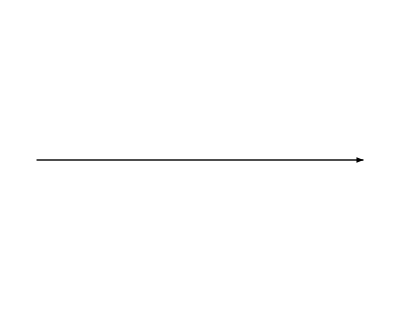
Geometric Objects | Graphs |  | 
-Graphics3D- | -Graphics- | -Graphics- | -Graphics-
Manifold | Regular Graph |  | k-Star
-Graphics3D- | -Graphics- | -Graphics- | -Graphics-
Orbifold | Orbigraph |  | Folded Directed k-Star

```mathematica
regHi={Style[1,Red],Style[{2,1<->2,3,1<->3,4,1<->4,5,1<->5},Thick,Blue]};
reg=HighlightGraph[SetProperty[ImportRegularGraphs[8,4]⟦3⟧,{VertexSize->0.2,EdgeStyle->Thick,ImageSize->150}],regHi];
regStar=SetProperty[HighlightGraph[StarGraph[5,VertexSize->0.2],regHi],ImageSize->150];

orbigHi={Style[4,Red],Style[{4->1,1,4->2,2,4->3,3},Thick,Blue]};
orbigLabels={
4->1->Placed["1",{0.6,{-0.5,0}}],
4->2->Placed["2",{1/2,{1.3,1.3}}],
4->3->Placed["1",{1/2,{1,0}}],
1->4->Placed["4",{0.4,{1.4,0}}],
2->4->Placed["4",{1/2,{0,0}}],
3->4->Placed["4",{1/2,{0,1.3}}]};
orbig=HighlightGraph[SetProperty[-Graphics-,
{VertexSize->0.2,
EdgeStyle->Thick,
ImageSize->150,
EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.1],
EdgeLabelStyle->16,
EdgeLabels->orbigLabels}],orbigHi];
orbiStarHi={Style[1,Red],Style[{2,1->2,3,1->3,4,1->4,5,1->5},Thick,Blue]};
orbiStarAdj={{0,2,1,1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}/.{0->∞};
orbiStar=SetProperty[HighlightGraph[WeightedAdjacencyGraph[orbiStarAdj,VertexSize->0.2,DirectedEdges->True],orbiStarHi],
{ImageSize->150,
EdgeShapeFunction->degenerateKStarEdges[orbiStarAdj],
GraphLayout->"RadialEmbedding"}];

labelText[str_]:=Text[Style[str,FontSize->20]];

bgColor=RGBColor[1,0.96,0.93];
Grid[
{{Text[Style["Geometric Objects",FontSize->24]],Text[Style["Graphs",FontSize->24]],SpanFromLeft,SpanFromLeft},
{sphere,reg,arrow,regStar},
{labelText["Manifold"],labelText["Regular Graph"],Null,labelText["k-Star"]},
{orbi,orbig,arrow,orbiStar},
{labelText["Orbifold"],labelText["Orbigraph"],Null,labelText["Folded Directed k-Star"]}},
Background->{{2->bgColor,3->bgColor,4->bgColor},None},
Spacings->{1,1},Frame->All,FrameStyle->RGBColor[0.96,0.96,0.96]]
```

(Original definition of orbigraphs due to Montes de Oca.)

## Spectral Geometry

```mathematica
ClearAll[r];
drumSolution[k_,l_,tf_,af_,r0_]:=Module[{μ=BesselJZero[k,l]/r0},tf[μ t0]af[k θ]BesselJ[k,μ r]//N];
drumPlot[t_,r0_]:=ParametricPlot3D[Evaluate@{r Cos[θ],r Sin[θ],drumSolution[1,1,Cos,Cos,r0]/.t0->t},
{r,0,r0},{θ,0,2π},
PlotRange->{-2,2},
ImageSize->300,
ViewPoint->{2.42,-1.61,1.72},
Axes->None,
Boxed->False];
period=4π/BesselJZero[1,1];
drumFrames=Table[Row@{drumPlot[t+(π/2)/3.831705970207512,1],drumPlot[t+(π/2)/1.915852985103756,2]},
{t,0,period,0.05}];
play=False;
EventHandler[Dynamic[n=Clock[{1,Length[drumFrames],1},2];drumFrames⟦If[play,n,1]⟧],"MouseDown":>(play=!play)]
```

## Classical Spectral Graph Theory

```mathematica
exReg=ImportRegularGraphs[8,3]⟦4⟧;
exRegAdj=AdjacencyMatrix@exReg;
regSpec=Sort[Eigenvalues@exRegAdj,Less];

exAdj={{0,1,1,2},{4,0,0,0},{4,0,0,0},{4,0,0,0}};
exOrbi=SetProperty[AdjacencyOrbigraph[exAdj],{EdgeLabelStyle->20,ImageSize->190,EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.1]}];
spec=Sort[Eigenvalues@exAdj,Less];

Grid[{
{exReg,arrow,MatrixForm@exRegAdj,arrow,TraditionalForm@regSpec},
{labelText["Regular Graph"],Null,labelText["Adjacency Matrix"],Null,labelText["Spectrum"]},
{exOrbi,arrow,MatrixForm@exAdj,arrow,TraditionalForm@spec},
{labelText["Orbigraph"],Null,labelText["Adjacency Matrix"],Null,labelText["Spectrum"]}},
Spacings->{2,2}]
```

-Graphics- | -Graphics- | (0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0) | -Graphics- | {-3,-1,-1,-1,1,1,1,3}
Regular Graph |  | Adjacency Matrix |  | Spectrum
-Graphics- | -Graphics- | (0 | 1 | 1 | 2
4 | 0 | 0 | 0
4 | 0 | 0 | 0
4 | 0 | 0 | 0) | -Graphics- | {-4,0,0,4}
Orbigraph |  | Adjacency Matrix |  | Spectrum

## Bounds on Singular Points

```mathematica
singularOrbigraphAdj={{0, 0, 0, 0, 1, 1, 0, 1},{0, 0, 1, 0, 0, 1, 1, 0},{0, 2, 0, 0, 1, 0, 0, 0},{0, 0, 0, 0, 1, 1, 1, 0},{1, 0, 1, 1, 0, 0, 0, 0},{1, 1, 0, 1, 0, 0, 0, 0},{0,1, 0, 2, 0, 0, 0, 0},{2, 0, 0, 0, 0, 0, 0, 1}};
singularPoints={3,7,8};
singularEdges=Flatten[Thread[#->First/@Position[singularOrbigraphAdj⟦#⟧,x_/;x>0]]&/@singularPoints];
singularHi=(Style[#,Red]&/@singularPoints)~Join~(Style[#,Blue]&/@singularEdges);
singularOrbi=SetProperty[HighlightGraph[AdjacencyOrbigraph@singularOrbigraphAdj,singularHi],{ImageSize->400,EdgeStyle->Lighter[Gray]}];

neighborhoods={{{0,2,1},{0,0,0},{0,0,0}},{{0,2,1},{0,0,0},{0,0,0}},{{1,2},{0,0}}};
singularNeighborhoods=HighlightGraph[SetProperty[AdjacencyOrbigraph[#],
{GraphLayout->"RadialEmbedding",ImageSize->200,EdgeShapeFunction->degenerateKStarEdges[#],EdgeLabels->None,VertexSize->0.1}],
{Style[1,Red],Style[1->2,Blue],Style[1->3,Blue],Style[1->1,Blue]}]&/@neighborhoods;

arrowDown=Item[Graphics[{Arrowheads[Large],Arrow[{{0,0},{0,-0.2}}]},PlotRange->{{-0.2,0.2},{0,-0.2}}],ItemSize->{30,0.1}];
spectrum=NumberForm[N[#],2]&/@Eigenvalues@singularOrbigraphAdj;

boundsSlide[hi_]:=Module[{hiItemTop,hiItemBottom},
hiItemTop={n,o}↦Item[o,Background->If[n==hi,bgColor,White],Frame->{{True,True},{False,True}},FrameStyle->If[n==hi,Black,White]];
hiItemBottom={n,o}↦Item[o,Background->If[n==hi,bgColor,White],Frame->{{True,True},{True,False}},FrameStyle->If[n==hi,Black,White]];
Grid[
{{hiItemTop[1,singularOrbi],arrow,hiItemTop[2,Column@singularNeighborhoods]},
{hiItemBottom[1,labelText["Orbigraph"]],Null,hiItemBottom[2,labelText["3 Singular Points"]]},
{Spacer[2]},
If[hi≥3,{hiItemTop[3,labelText["Spectrum"]],Null,hiItemTop[4,labelText["Bound from Spectrum"]]},{}],
If[hi≥3,{hiItemBottom[3,spectrum],arrow,hiItemBottom[4,labelText["1 ≤ (# Singular Points) ≤ 3"]]},{}]},
Spacings->{1,1}]];
boundsSlide[1]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics-
-Graphics-
Orbigraph |  | 3 Singular Points
 |  | 
 |  | 
 |  |

## Bounds on Singular Points

```mathematica
boundsSlide[2]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics-
-Graphics-
Orbigraph |  | 3 Singular Points
 |  | 
 |  | 
 |  |

## Bounds on Singular Points

```mathematica
boundsSlide[3]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics-
-Graphics-
Orbigraph |  | 3 Singular Points
 |  | 
Spectrum |  | Bound from Spectrum
{3.,-2.6,-2.1,2.,-1.1,0.82+0.15 ⅈ,0.82-0.15 ⅈ,0.23} | -Graphics- | 1 ≤ (# Singular Points) ≤ 3

## Bounds on Singular Points

```mathematica
boundsSlide[4]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics-
-Graphics-
Orbigraph |  | 3 Singular Points
 |  | 
Spectrum |  | Bound from Spectrum
{3.,-2.6,-2.1,2.,-1.1,0.82+0.15 ⅈ,0.82-0.15 ⅈ,0.23} | -Graphics- | 1 ≤ (# Singular Points) ≤ 3

## Bounds on Singular Points

Theorem (Spectral Bounds on Singular Points, G.-Stanhope-S. 2013):

If Γ is a k-orbigraph on n vertices and spec(Γ)=λ_1,…,λ_n we have

(∑_i λ_i^2-n k)/(k^2-k)≤s≤∑_i λ_i^2-n k.

Corollary:

If Γ is a k-orbigraph on n vertices then Γ is isomorphic to an undirected k-regular graph if and only if

∑_i λ_i^2-n k=0 and ∑_i λ_i=1.